Clear the memory of all variables and values

```mathematica
ClearAll["Global`*"]
```

specify cost and constraint functions

```mathematica
P=2*7833*5*Pi*x2*x1; (* Tube mass where x1 it t and x2 is R *)
fact=1.00; (* up to 2.5 is good, down to 0.65 is good *)
g1=10*10^6/(2*Pi*x2*x1)-248*10^6*fact; (* stress constraint *)
g2=10*10^6-(Pi^3*(207*10^9)*x2^3*x1)/(4*5*5); (* buckling constraint *)
g3=-x2; (* non-negativity constraint *)
g4=-x1; (* non-negativity constraint *)
```

specify the plot ranges for the design variables

```mathematica
x1L=0;
x1U=0.1;
x2L=0;
x2U=0.3;
```

specify the title of the plot

```mathematica
titleplot="Tube Column Problem"
```

Tube Column Problem

Plot the constraint boundary for g1 constraint

```mathematica
Plotg1=ContourPlot[g1,{x1,x1L,x1U},{x2,x2L,x2U}, ContourShading->False, Contours->{0}, ContourStyle->{{Thickness[0.01]}}, AxesLabel->{"x1","x2"},Axes->True, PlotLabel->titleplot,ImageSize->290,PlotRange->{{-0.01*x1U,x1U},{-0.01*x2U,x2U}}];
```

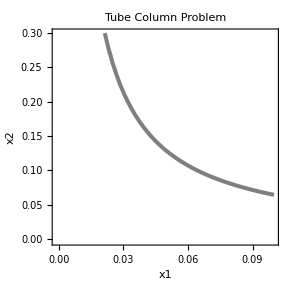

```mathematica
Show[Plotg1]
```

Identify the infeasible and feasible side of constraint g1

```mathematica
x1g1infeas=0.06;
x2g1infeas=0.06;
testg1=g1/.{x1->x1g1infeas,x2->x2g1infeas}
g1test1pt=Graphics[{PointSize[Medium],Red,Point[{x1g1infeas,x2g1infeas}]}];
```

1.94097×10^8

```mathematica
x1g1feas=0.06;
x2g1feas=0.2;
testg1=g1/.{x1->x1g1feas,x2->x2g1feas}
g1test2pt=Graphics[{PointSize[Medium],Blue,Point[{x1g1feas,x2g1feas}]}];
```

-1.15371×10^8

Plot constraint boundary, infeasible and feasible points for g1, and g1 constraint shading (which should be on infeasible side)

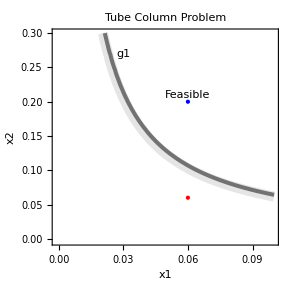

```mathematica
Plotg1=ContourPlot[g1,{x1,x1L,x1U},{x2,x2L,x2U}, ContourShading->False, Contours->{0,10000000.85}, ContourStyle->{{Thickness[0.01]},{GrayLevel[0.8],Thickness[0.025]}}];

Show[Plotg1,g1test1pt,g1test2pt,AxesLabel->{"x1","x2"},Axes->True, PlotLabel->titleplot,Epilog->{Text["g1",{0.03,0.27}], Text["Feasible",{x1g1feas,x2g1feas+.01}]},ImageSize->290,PlotRange->{{-0.01*x1U,x1U},{-0.01*x2U,x2U}}]
```

You will need to plot the other constraints, identify their feasible and infeasible regions, and identify the overall feasible region.

```mathematica
x1feas=0.06;
x2feas=0.2;
feaspoint=Graphics[{PointSize[Medium],Magenta,Point[{x1feas,x2feas}]}];
```

Pick contour values for cost function contour (you need at least 6)

```mathematica
cont1=500;
cont2=1000;
cont3=1500;
```

```mathematica
PlotP=ContourPlot[P,{x1,x1L,x1U},{x2,x2L,x2U}, ContourShading->False, Contours->{cont1,cont2,cont3}, ContourStyle->{{Dashing[{0.03,0.04}],Thickness[0.007],Blue},{Dashing[{0.03,0.04}],Thickness[0.007],Green},{Dashing[{0.03,0.04}],Thickness[0.007],Orange}}];
```

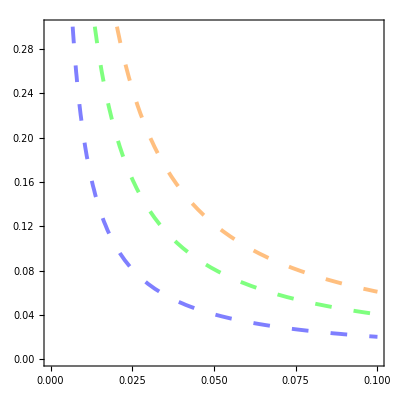

```mathematica
Show[PlotP]
```

Plotting contour legend values

```mathematica
contftext=ToString["f="];
cont1text=TextString[Row[{contftext ,cont1}]]
```

f=500

```mathematica
cont2text=TextString[Row[{contftext ,cont2}]];
cont3text=TextString[Row[{contftext ,cont3}]];
```

Plotting contour legend location in plot region, base is the bottom contour, shift is how much each subsequent contour is shifted from the previous contour legend

```mathematica
xfbase=0.09;
xfshift=0;
yfbase=0.12;
yfshift=0.015;
```

Combining constraints and contour plots

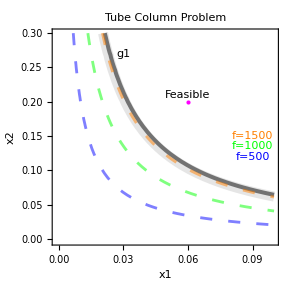

```mathematica
Show[Plotg1,PlotP,feaspoint,AxesLabel->{"x1","x2"},Axes->True, PlotLabel->titleplot,Epilog->{Text["g1",{0.03,0.27}], Text["Feasible",{x1feas,x2feas+.01}] , {Blue,Text[cont1text,{xfbase,yfbase}]},  {Green,Text[cont2text,{xfbase+xfshift,yfbase+yfshift}]},  {Orange,Text[cont3text,{xfbase+2*xfshift,yfbase+2*yfshift}]}},ImageSize->290,PlotRange->{{-0.01*x1U,x1U},{-0.01*x2U,x2U}}]
```

Plot the final plot with the solution point or with the end points and highlighted solution region as shown in the example

```mathematica
x1Apt=0.029;
x2Apt=0.22;

x1Bpt=0.06;
x2Bpt=0.108;

(* if cost function is parallel to portion of g1 constraint *)
HighPlot=ContourPlot[g1,{x1,x1Apt,x1Bpt},{x2,x2Bpt,x2Apt}, ContourShading->False, Contours->{0}, ContourStyle->{{Thickness[0.05],Magenta}}];
```

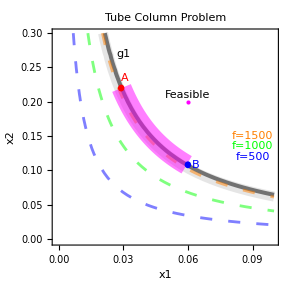

```mathematica
Show[Plotg1,PlotP,feaspoint,HighPlot,AxesLabel->{"x1","x2"},Axes->True, PlotLabel->titleplot,Epilog->{Text["g1",{0.03,0.27}],Text["Feasible",{x1feas,x2feas+.01}] , {Blue,Text[cont1text,{xfbase,yfbase}]},  {Green,Text[cont2text,{xfbase+xfshift,yfbase+yfshift}]},  {Orange,Text[cont3text,{xfbase+2*xfshift,yfbase+2*yfshift}]},{Red,Text["A",{x1Apt+0.0015,x2Apt+0.015}]}, {Red,Disk[{x1Apt,x2Apt},{0.0015,0.005}]}, {Blue,Text["B",{x1Bpt+0.0035,x2Bpt}]}, {Blue,Disk[{x1Bpt,x2Bpt},{0.0015,0.005}]}},ImageSize->290,PlotRange->{{-0.01*x1U,x1U},{-0.01*x2U,x2U}}]
```